## Two kings and a piece

## Code

```mathematica
(*n=size of the board*)
(*position = {{white king x, white king y}, {black king x, black king y}, {piece x, piece y} ({-1,-1} if the piece was taken), 1->white's move; 0->black's move, name of the piece}*)
```

```mathematica
flipVertically[{{w1_,w2_},{b1_,b2_},{-1,-1},m_,f_},n_]:={{n+1-w1,w2},{n+1-b1,b2},{-1,-1},m,f};
flipVertically[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_,f_},n_]:={{n+1-w1,w2},{n+1-b1,b2},{n+1-r1,r2},m,f};
flipHorizontally[{{w1_,w2_},{b1_,b2_},{-1,-1},m_,f_},n_]:={{w1,n+1-w2},{b1,n+1-b2},{-1,-1},m,f};
flipHorizontally[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_,f_},n_]:={{w1,n+1-w2},{b1,n+1-b2},{r1,n+1-r2},m,f};
flipDiagonally[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_,f_},n_]:={{w2,w1},{b2,b1},{r2,r1},m,f};
toStandardPosition[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_,f_},n_]:=Module[{ans={{w1,w2},{b1,b2},{r1,r2},m,f}},
If[ans[[3]]=={-1,-1},ans[[5]]="none"];
If[ans[[5]]=="none",ans[[3]]={-1,-1}];
If[f!="pawn",
If[w1>Ceiling[n/2],ans=flipVertically[ans,n]];
If[ans[[1,2]]>Ceiling[n/2],ans=flipHorizontally[ans,n]];
If[ans[[1,1]]>ans[[1,2]],ans=flipDiagonally[ans,n]];
If[ans[[1,1]]==ans[[1,2]]&&ans[[2,2]]>ans[[2,1]],ans=flipDiagonally[ans,n]];
If[OddQ[n]&&ans[[1,2]]==Ceiling[n/2]&&ans[[2,2]]>Ceiling[n/2],ans=flipHorizontally[ans,n]];
If[ans[[1,1]]==ans[[1,2]]&&ans[[2,2]]==ans[[2,1]]&&ans[[3,1]]>ans[[3,2]],ans=flipDiagonally[ans,n]];
If[OddQ[n]&&ans[[1,2]]==Ceiling[n/2]&&ans[[2,2]]==Ceiling[n/2]&&ans[[3,2]]>Ceiling[n/2],ans=flipHorizontally[ans,n]],

If[ans[[1,2]]>Ceiling[n/2],ans=flipHorizontally[ans,n]];
];
ans
];(*if there is no pawn (no cpecific direction up the board):
white king ends up in the eights (w1<n/2, w2<n/2, w1>=w2), 
if the white king is on the main diagonal, then black king ends up in the half (b2>=b1),
if n is odd and w2==Ceiling[n/2], then black king ends up in the half (b2<=n/2),
if both kings are on the diagonal, the rook ends up in the half (r2>r1),
if n is odd and w2==Ceiling[n/2] and b2==Ceiling[n/2], then black rook ends up in the half (r2<=n/2)

if there is a pawn, the white king ends up in the half (w2<n/2)

if the piece is at {-1,-1}, its name is "none" and vice versa*)
```

```mathematica
kingMoves[x_,y_,n_]:=Module[{possible,legal},
	possible=Table[
		{x+dx,y+dy},
		{dx,-1,1},
		{dy,-1,1}
	];
	possible=Flatten[possible,1];
	legal=DeleteCases[possible,{0|n+1,_}|{_,0|n+1}|{x,y}];
	legal
];(*returns a list of valid moves for a single king*)
```

```mathematica
knightMoves[x_,y_,n_]:=DeleteCases[{{x+2,y+1},{x+1,y+2},{x-2,y+1},{x-1,y+2},{x+2,y-1},{x+1,y-2},{x-2,y-1},{x-1,y-2}},{a_,b_}/;(a<1||b<1||a>n||b>n)];
```

```mathematica
bishopMoves[x_,y_,n_]:=DeleteCases[Join[{x+#,y+#}&/@Range[-n,n],{x+#,y-#}&/@Range[-n,n]],{a_,b_}/;(a<1||b<1||a>n||b>n||(a==x&&b==y))];(*can be optimized*)
```

```mathematica
rookMoves[x_,y_,n_]:=DeleteCases[Join[{#,y}&/@Range[n],{x,#}&/@Range[n]],{x,y}];(*returns a list of valid moves for a single rook*)
```

```mathematica
queenMoves[x_,y_,n_]:=Join[rookMoves[x,y,n],bishopMoves[x,y,n]];
```

```mathematica
validPosition[{{w1_,w2_},{b1_,b2_},{f1_,f2_},m_,f_},n_]:=Module[{ans=True},
If[Abs[w1-b1]<=1&&Abs[w2-b2]<=1,ans=False];
If[f1!=-1&&((w1==f1&&w2==f2)||(b1==f1&&b2==f2)),ans=False];
If[m==1&&f=="pawn"&&({b1,b2}=={f1+1,f2-1}||{b1,b2}=={f1+1,f2+1}),ans=False];
If[m==1&&f=="knight"&&MemberQ[knightMoves[f1,f2,n],{b1,b2}],ans=False];
If[m==1&&(f=="bishop"||f=="queen")&&((f1-b1==f2-b2&&(f1-w1!=f2-w2||w2<Min[b2,f2]||w2>Max[b2,f2]))||(f1-b1==-f2+b2&&(f1-w1!=-f2+w2||w2<Min[b2,f2]||w2>Max[b2,f2]))),ans=False];
If[m==1&&(f=="rook"||f=="queen")&&((f1==b1&&(w1!=b1||w2<Min[b2,f2]||w2>Max[b2,f2]))||(f2==b2&&(w2!=b2||w1<Min[b1,f1]||w1>Max[b1,f1]))),ans=False];
ans
];
```

```mathematica
nextPositions[{{w1_,w2_},{b1_,b2_},{f1_,f2_},m_,f_},n_]:=Module[{ans={}},
If[m==1,(*white's move*)
If[f=="pawn",
If[f1==n-1,
ans={{w1,w2},{b1,b2},{f1+1,f2},0,#}&/@{"knight","bishop","rook","queen"},
ans={{{w1,w2},{b1,b2},{f1+1,f2},0,"pawn"}}]
];
If[f=="knight",ans={{w1,w2},{b1,b2},#,0,f}&/@knightMoves[f1,f2,n]];
If[f=="bishop"||f=="queen",
ans=Join[ans,DeleteCases[{{w1,w2},{b1,b2},#,0,f}&/@bishopMoves[f1,f2,n],
p_/;(f1-p[[3,1]]==f2-p[[3,2]]&&w1-f1==w2-f2&&Sign[w2-f2]!=Sign[w2-p[[3,2]]])||
(f1-p[[3,1]]==-f2+p[[3,2]]&&w1-f1==-w2+f2&&Sign[w2-f2]!=Sign[w2-p[[3,2]]])||
(f1-p[[3,1]]==f2-p[[3,2]]&&b1-f1==b2-f2&&Sign[b2-f2]!=Sign[b2-p[[3,2]]])||
(f1-p[[3,1]]==-f2+p[[3,2]]&&b1-f1==-b2+f2&&Sign[b2-f2]!=Sign[b2-p[[3,2]]])
]]
];
If[f=="rook"||f=="queen",
ans=Join[ans,DeleteCases[{{w1,w2},{b1,b2},#,0,f}&/@rookMoves[f1,f2,n],
p_/;(f1==p[[3,1]]&&w1==f1&&Sign[w2-f2]!=Sign[w2-p[[3,2]]])||
(f2==p[[3,2]]&&w2==f2&&Sign[w1-f1]!=Sign[w1-p[[3,1]]])||
(f1==p[[3,1]]&&b1==f1&&Sign[b2-f2]!=Sign[b2-p[[3,2]]])||
(f2==p[[3,2]]&&b2==f2&&Sign[b1-f1]!=Sign[b1-p[[3,1]]])
]](*to avoid the rook leaping over one of the kings*)
];
ans=Join[ans,{#,{b1,b2},{f1,f2},0,f}&/@kingMoves[w1,w2,n]],
(*black's move*)
ans={{w1,w2},#,{f1,f2},1,f}&/@kingMoves[b1,b2,n];
ans=ans/.{{a_,b_},{c_,d_},{c_,d_},1,e_}->{{a,b},{c,d},{-1,-1},1,"none"}
];
ans=DeleteCases[ans,p_/; validPosition[p,n]==False];
DeleteDuplicates[toStandardPosition[#,n]&/@ans]
];
```

```mathematica
edgesFromPosition[p_,n_]:={p->#}&/@nextPositions[p,n];
```

```mathematica
generatePositions[n_]:=DeleteDuplicates[toStandardPosition[#,n]&/@DeleteCases[Join[
Flatten[Table[{{w1,w2},{b1,b2},{r1,r2},m,f},{w1,n},{w2,n},{b1,n},{b2,n},{r1,n},{r2,n},{m,0,1},{f,{"knight","bishop","rook","queen"}}],7],
Flatten[Table[{{w1,w2},{b1,b2},{r1,r2},m,"pawn"},{w1,n},{w2,n},{b1,n},{b2,n},{r1,2,n-1},{r2,n},{m,0,1}],6],
Flatten[Table[{{w1,w2},{b1,b2},{-1,-1},m,"none"},{w1,n},{w2,n},{b1,n},{b2,n},{m,0,1}],4]
],
p_/; validPosition[p,n]==False
]];(*all possible positions*)
```

```mathematica
isItTerminal[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_,f_},n_]:=Length[nextPositions[{{w1,w2},{b1,b2},{r1,r2},m,f},n]]==0;
```

```mathematica
isItCheck[{{w1_,w2_},{b1_,b2_},{r1_,r2_},m_,f_},n_]:=!validPosition[{{w1,w2},{b1,b2},{r1,r2},1-m,f},n];
```

```mathematica
pawnGamesWinning[n_]:=Module[{pos,ans,pawnSafelyPromotes,stalemates,pawnCanBeCaptured,step,myNextPositions,listContainsWins,listContainsDraws,listDecided},
pos=DeleteDuplicates[toStandardPosition[#,n]&/@DeleteCases[
Flatten[Table[{{w1,w2},{b1,b2},{r1,r2},m,"pawn"},{w1,n},{w2,n},{b1,n},{b2,n},{r1,2,n-1},{r2,n},{m,0,1}],6],
p_/; validPosition[p,n]==False
]];
myNextPositions[p_]:=DeleteCases[nextPositions[p,n],a_/;a[[5]]!="pawn"];
pawnSafelyPromotes=Select[pos,(!isItTerminal[#,3])&&#[[4]]==1&&#[[3,1]]==n-1&&(Abs[#[[2,1]]-n]>1||Abs[#[[2,2]]-#[[3,2]]]>1||(Abs[#[[1,1]]-n]<=1&&Abs[#[[1,2]]-#[[3,2]]]<=1))&];
stalemates=Select[pos,isItTerminal[#,3]&];
pawnCanBeCaptured=Select[pos,#[[4]]==0&&Abs[#[[2,2]]-#[[3,2]]]<=1&&Abs[#[[2,2]]-#[[3,2]]]<=1&&(Abs[#[[1,1]]-#[[3,1]]]>1||Abs[#[[1,2]]-#[[3,2]]]>1)&];
ans=Join[AssociationThread[pawnSafelyPromotes,Table["win",Length@pawnSafelyPromotes]],AssociationThread[stalemates,Table["draw",Length@stalemates]],AssociationThread[pawnCanBeCaptured,Table["draw",Length@pawnCanBeCaptured]]];
listContainsWins[assoc_,list_]:=MemberQ[Values@KeyTake[assoc,list],"win"];
listContainsDraws[assoc_,list_]:=MemberQ[Values@KeyTake[assoc,list],"draw"];
listDecided[assoc_,list_]:=SubsetQ[Keys[assoc],list];
step[assoc_]:=With[{towin=Select[pos,(!KeyExistsQ[assoc,#])&&((#[[4]]==1&&listContainsWins[assoc,myNextPositions[#]])||(#[[4]]==0&&(!listContainsDraws[assoc,myNextPositions[#]])&&listDecided[assoc,myNextPositions[#]]))&],todraw=Select[pos,(!KeyExistsQ[assoc,#])&&((#[[4]]==0&&listContainsDraws[assoc,myNextPositions[#]])||(#[[4]]==1&&(!listContainsWins[assoc,myNextPositions[#]])&&listDecided[assoc,myNextPositions[#]]))&]},
Join[assoc,AssociationThread[towin,Table["win",Length@towin]],AssociationThread[todraw,Table["draw",Length@todraw]]]
];
FixedPoint[step[#]&,ans]
];
```

```mathematica
evaluationOfPositions[n_]:=Module[{pos=generatePositions[n],ans,stalemates,nkb(*none or knight or bishop*),pieceCanBeCaptured,qr(*queen or rook, not stalemate, not about to be captured*)},
stalemates=Select[pos,isItTerminal[#,n]&&(!isItCheck[#,n])&];
nkb=Select[pos,#[[5]]=="none"||#[[5]]=="knight"||#[[5]]=="bishop"&];
pieceCanBeCaptured=Select[pos,#[[4]]==0&&Abs[#[[2,2]]-#[[3,2]]]<=1&&Abs[#[[2,2]]-#[[3,2]]]<=1&&(Abs[#[[1,1]]-#[[3,1]]]>1||Abs[#[[1,2]]-#[[3,2]]]>1)&];(*black to move, the piece is unprotected and can be captured*)
qr=Select[pos,(#[[5]]=="queen"||#[[5]]=="rook")&&((!(isItTerminal[#,n]&&(!isItCheck[#,n]))&&!(#[[4]]==0&&Abs[#[[2,2]]-#[[3,2]]]<=1&&Abs[#[[2,2]]-#[[3,2]]]<=1&&(Abs[#[[1,1]]-#[[3,1]]]>1||Abs[#[[1,2]]-#[[3,2]]]>1))))&];
Join[pawnGamesWinning[n],AssociationThread[stalemates,Table["draw",Length@stalemates]],AssociationThread[nkb,Table["draw",Length@nkb]],AssociationThread[pieceCanBeCaptured,Table["draw",Length@pieceCanBeCaptured]],AssociationThread[qr,Table["win",Length@qr]]]
];
```

```mathematica
generateInitialPosition[n_]:=Module[{ans={{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-3]+2,RandomInteger[n-1]+1},1,"pawn"}},
While[!validPosition[ans,n],
ans={{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-1]+1,RandomInteger[n-1]+1},{RandomInteger[n-3]+2,RandomInteger[n-1]+1},1,"pawn"}
];
toStandardPosition[ans,n]
];(*we start with a pawn, the pawn is not on the last rank and not on the first rank, it is not mate (of course it's not mate), not stalemate, and it's white to move*)
```

```mathematica
generateRandomWalkResult[n_]:=With[{cur=generateInitialPosition[n]},
NestWhile[RandomChoice[nextPositions[#,n]]&,cur,(!isItTerminal[#,n])&&(#[[5]]!="none")&]
];
```

```mathematica
generateRandomWalk[n_]:=With[{cur=generateInitialPosition[n]},
NestWhileList[RandomChoice[nextPositions[#,n]]&,cur,(!isItTerminal[#,n])&&(#[[5]]!="none")&]
];
```

```mathematica
generateEdges[positions_,n_]:=Flatten[edgesFromPosition[#,n]&/@positions,2];
```

```mathematica
MakeBoxes[position:ChessPosition[{{w1_,w2_},{b1_,b2_},{f1_,f2_},m_,f_},n_],form:StandardForm]:=Module[{table=Table[" ",{i,n},{j,n}],grid},
table[[n-w1+1,w2]]=♔;
table[[n-b1+1,b2]]=♚;
If[f1!=-1,table[[n-f1+1,f2]]=Switch[f,"pawn","♙","knight","♘","bishop","♗","rook","♖","queen","♕"]];
grid=Grid[table,Dividers->All,ItemSize->{1.,1.},
Background->{Automatic,Automatic,Flatten[Table[{i,j}->If[EvenQ[i+j],LightGray,White],{i,n},{j,n}]]}];
ToBoxes@Interpretation[grid,position]
]
```

```mathematica
positionToGrid[{{w1_,w2_},{b1_,b2_},{f1_,f2_},m_,f_},n_]:=Module[{table=Table[" ",{i,n},{j,n}],grid},
table[[n-w1+1,w2]]=♔;
table[[n-b1+1,b2]]=♚;
If[f1!=-1,table[[n-f1+1,f2]]=Switch[f,"pawn","♙","knight","♘","bishop","♗","rook","♖","queen","♕"]];
grid=Grid[table,Dividers->All,ItemSize->{1.,1.},
Background->{Automatic,Automatic,Flatten[Table[{i,j}->If[EvenQ[i+j],LightGray,White],{i,n},{j,n}]]}];
grid
];
```

```mathematica
ChessPositionData[ChessPosition[data_,n_]]:=data;
```

```mathematica
generateLabels[positions_,n_]:=#->Placed[ChessPosition[#,n],Tooltip]&/@positions;
```

```mathematica
colorFunction[p_,n_]:=If[!isItTerminal[p,n],
Switch[p[[5]],"none",Black,"pawn",Gray,"knight",Green,"bishop",Lighter[Pink],"rook",Cyan,"queen",Magenta],(*not mate, not stalemate*)
If[isItCheck[p,n],Red,(*mate*)
Yellow(*stalemate*)
]
];
```

```mathematica
generateVertexStyle[positions_,n_]:=#->{colorFunction[#,n]}&/@positions;
```

```mathematica
showGraph[n_]:=With[{positions=generatePositions[n]},
Legended[Graph[
generateEdges[positions,n],
VertexStyle->generateVertexStyle[positions,n],
VertexLabels->generateLabels[positions,n],
GraphLayout->"SpringElectricalEmbedding",
ImageSize->1000,
VertexShapeFunction->(Normal[evaluationOfPositions[n]]/.{(a_->"win")->(a->"Square"),(a_->"draw")->(a->"Circle")}),
EdgeStyle->Arrowheads[Small],
VertexSize->1.5(n-2)
],
PointLegend[{Black,Black,Red,Yellow,Gray,Green,Lighter[Pink],Cyan,Magenta,Black},{"draw","win for white","mate","stalemate","pawn","knight","bishop","rook","queen","the piece was captured"},LegendMarkers->{{"○",20},{"□",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20}},LegendMarkerSize->20]]
];
```

```mathematica
generateGraph[n_]:=With[{positions=generatePositions[n]},
Graph[generateEdges[positions,n],
VertexStyle->generateVertexStyle[positions,n],
VertexLabels->generateLabels[positions,n],
GraphLayout->"SpringElectricalEmbedding",
ImageSize->1000,
VertexShapeFunction->(Normal[evaluationOfPositions[n]]/.{(a_->"win")->(a->"Square"),(a_->"draw")->(a->"Circle")}),
EdgeStyle->Arrowheads[Small],
VertexSize->1.5(n-2)
]
];
```

```mathematica
showGraphWithoutPawn[n_]:=With[{positions=DeleteCases[generatePositions[n],p_/;p[[5]]=="pawn"]},
Legended[Graph[
generateEdges[positions,n],
VertexStyle->generateVertexStyle[positions,n],
VertexLabels->generateLabels[positions,n],
GraphLayout->"SpringElectricalEmbedding",
ImageSize->1000,
VertexShapeFunction->(Normal[KeySelect[evaluationOfPositions[n],#[[5]]!="pawn"&]]/.{(a_->"win")->(a->"Square"),(a_->"draw")->(a->"Circle")}),
EdgeStyle->Arrowheads[Small],
VertexSize->n-2
],
PointLegend[{Black,Black,Red,Yellow,Green,Lighter[Pink],Cyan,Magenta,Black},{"draw","win for white","mate","stalemate","knight","bishop","rook","queen","the piece was captured"},LegendMarkers->{{"○",20},{"□",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20}},LegendMarkerSize->20]]
];
```

```mathematica
showWalk[graph_,walk_]:=
Legended[HighlightGraph[graph,Join[Style[#,Thickness[0.004],Red,Arrowheads[0.02]]&/@Thread[Most[walk]->Rest[walk]]]],PointLegend[{Black,Black,Red,Yellow,Green,Lighter[Pink],Cyan,Magenta,Black},{"draw","win for white","mate","stalemate","knight","bishop","rook","queen","the piece was captured"},LegendMarkers->{{"○",20},{"□",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20}},LegendMarkerSize->20]]
```

```mathematica
generateResults[n_,k_]:=Table[generateRandomWalkResult[n],k];
```

```mathematica
generateResultsGraph[n_]:=With[{positions=generatePositions[n]},
Legended[Graph[
generateEdges[positions,n],
VertexStyle->generateVertexStyle[positions,n],
VertexLabels->generateLabels[positions,n],
VertexSize->(findExpectanciesPerNode[n]/.(p_->s_)->(p->0.3Log[1+1000s])),
EdgeStyle->Arrowheads[Small],
ImageSize->1500,
VertexShapeFunction->(Normal[evaluationOfPositions[n]]/.{(a_->"win")->(a->"Square"),(a_->"draw")->(a->"Circle")})
],
PointLegend[{Black,Black,Red,Yellow,Green,Lighter[Pink],Cyan,Magenta,Black},{"draw","win for white","mate","stalemate","knight","bishop","rook","queen","the piece was captured"},LegendMarkers->{{"○",20},{"□",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20},{"◆",20}},LegendMarkerSize->20]]
];
```

```mathematica
winningProbability[n_]:=With[{exp=findExpectanciesPerNode[n]},
Total[exp/.(p_->e_)->If[isItCheck[p,n]&&isItTerminal[p,n],e,0]]/Total[exp[[All,2]]]
];
```

```mathematica
degeneracy[p_,n_]:=If[p[[5]]!="pawn",Length[DeleteDuplicates[{p,flipHorizontally[p,n],flipVertically[p,n],flipDiagonally[p,n],flipHorizontally[flipDiagonally[p,n],n],flipVertically[flipDiagonally[p,n],n],flipHorizontally[flipVertically[p,n],n],flipDiagonally[flipHorizontally[flipVertically[p,n],n],n]}]],
Length[DeleteDuplicates[{p,flipHorizontally[p,n]}]]
];(*how many non-standardized states correspond to this (standardized) position p*)
```

```mathematica
findExpectanciesPerNode[n_]:=Module[{positions=generatePositions[n],sa,totalInitialPositions,degeneracies,positionToIndex,genCol,rightPart},
degeneracies=degeneracy[#,n]&/@positions;
positionToIndex=Association[Thread[positions->Range[Length[positions]]]];
totalInitialPositions=Total[If[isItTerminal[#,n]||#[[5]]!="pawn",0,degeneracy[#,n]]&/@positions];
genCol[p_]:=With[{nextPos=nextPositions[p,n]},
If[isItTerminal[p,n]||p[[5]]=="none",{},{positionToIndex[#],positionToIndex[p]}->-1./Length[nextPos]&/@nextPos]
];
sa=SparseArray[Flatten[Join[genCol[#]&/@positions,{#,#}->1.&/@Range[Length[positions]]]]];
rightPart=If[isItTerminal[#,n]||#[[5]]!="pawn",0.,N[degeneracy[#,n]]/totalInitialPositions]&/@positions;
Thread[positions->N@LinearSolve[sa,rightPart]]
];(*if a new random walk is born from a pawn position every move (taking the degeneracy of nodes into account), what is the expectancy of number of walks that are currently in this vertex*)
```

```mathematica
generateTree[n_,maxLevel_]:=With[{root=ChessPosition[{{1,Ceiling[n/2]},{3,Ceiling[n/2]},{2,Ceiling[n/2]},1,"pawn"},n]},
NestTree[Map[ChessPosition[#,n]&,nextPositions[ChessPositionData[#],n]]&,root,maxLevel,BaseStyle->{Black,Thick},TreeElementStyle->All->Opacity[0],ImageSize->{400*n^3,150*maxLevel}]
];
```

```mathematica
multiwayGraph[n_,maxLevel_]:=Module[{root={{{1,Ceiling[n/2]},{3,Ceiling[n/2]},{2,Ceiling[n/2]},1,"pawn"},1},edges={},vertexStyle,curLayer,nextLayer,genEdgesForThisVertex,labels},
curLayer={root};
labels={root->Rasterize[positionToGrid[root[[1]],n]]};
genEdgesForThisVertex[{p_,k_}]:={p,k}->{#,k+1}&/@nextPositions[p,n];
For[i=1,i<=maxLevel,i++,
edges=Join[edges,Flatten[genEdgesForThisVertex[#]&/@curLayer]];
nextLayer=Flatten[DeleteDuplicates[Join[nextPositions[#[[1]],n],1]]&/@curLayer,1];
curLayer={#,i+1}&/@nextLayer;
labels=Join[labels,#->Rasterize[positionToGrid[#[[1]],n]]&/@curLayer];
];
edges=DeleteDuplicates[edges];
Graph[edges,GraphLayout->{"LayeredEmbedding","RootVertex"->root,"LeafDistance"->0.7},VertexShape->labels,VertexSize->0.6,EdgeStyle->Arrowheads[Small],ImageSize->150*Length[curLayer]]
];(*vertices include the information about the number of moves, vertex={position, move number}*)
```

## Graphs of positions

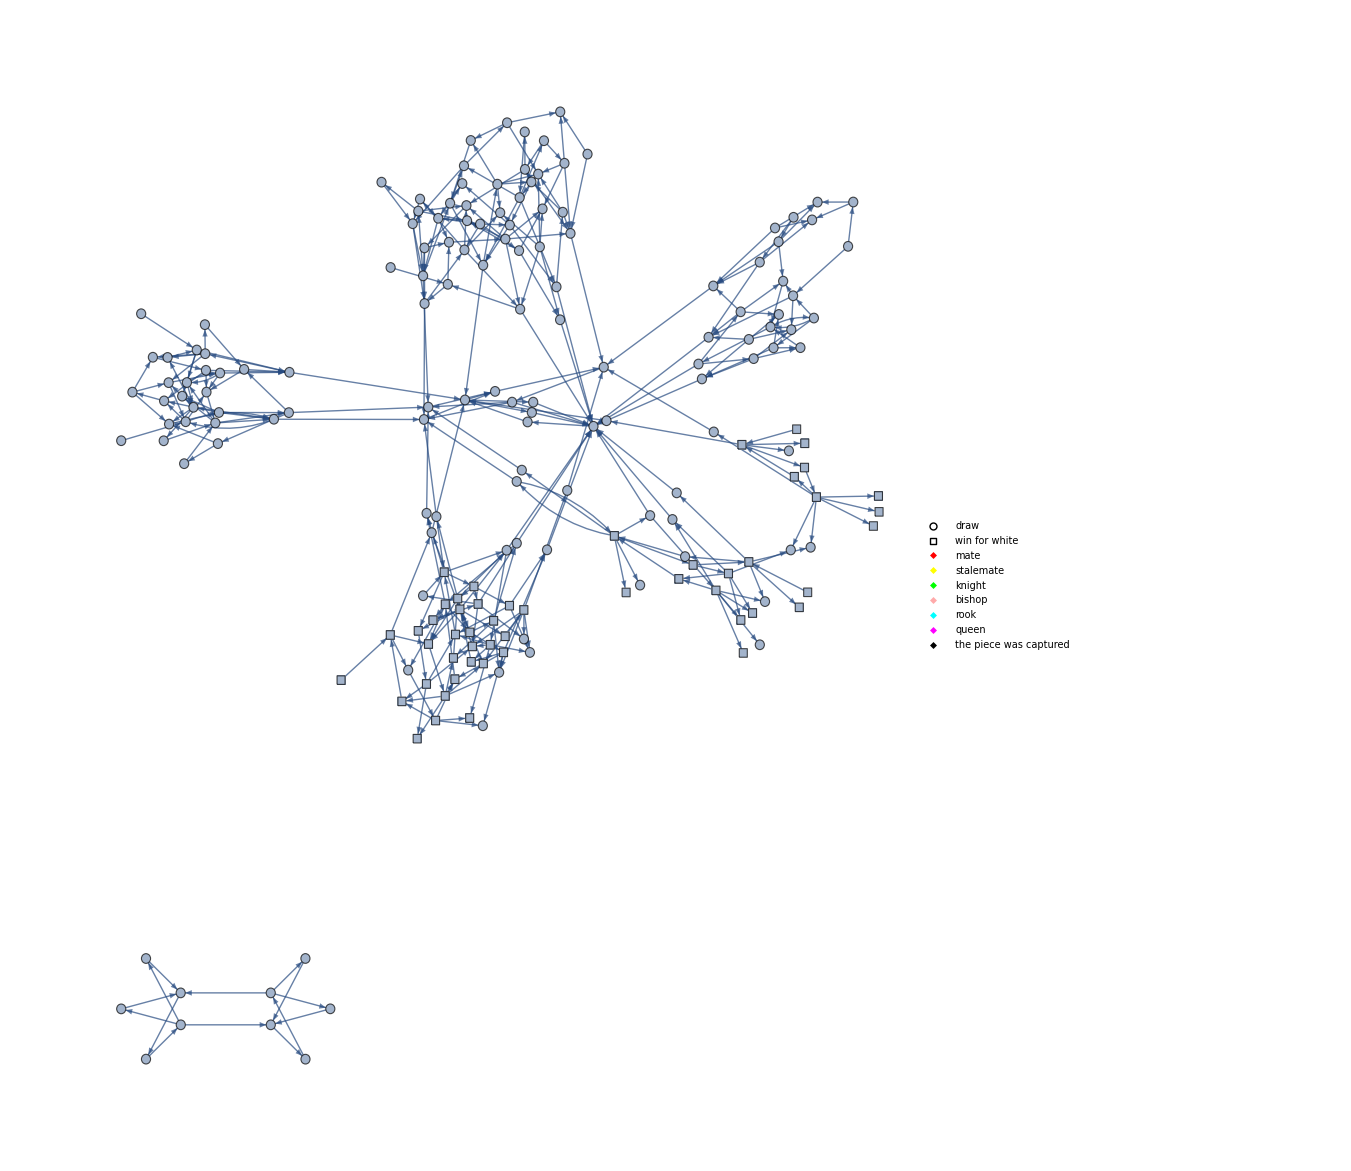

```mathematica
showGraphWithoutPawn[3]
```

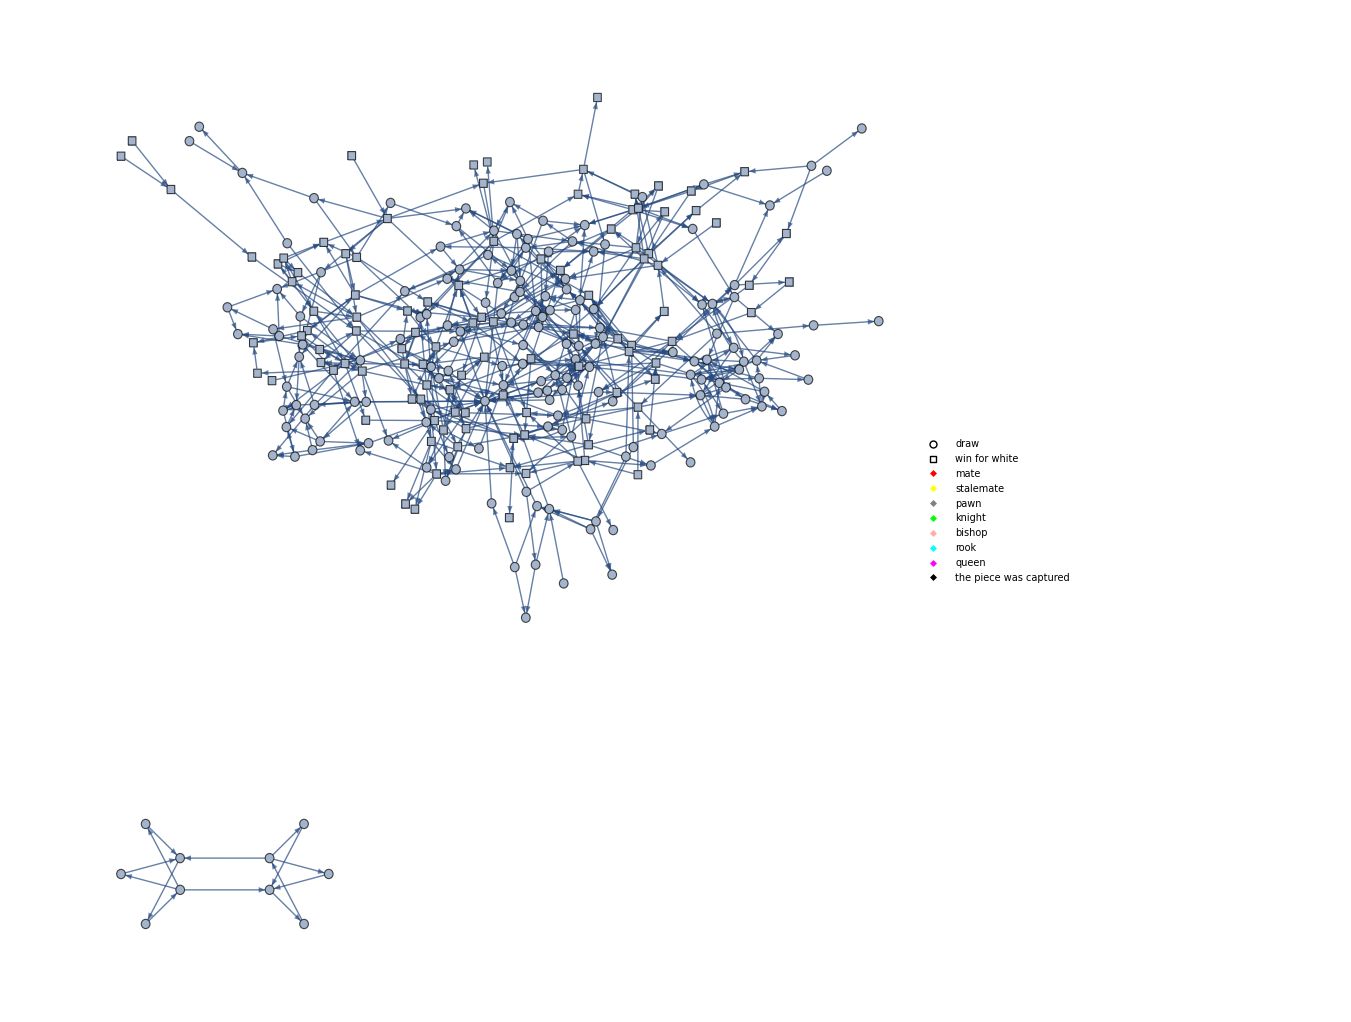

```mathematica
showGraph[3]
```

## Random walks and the density of walks per node

```mathematica
graph=generateGraph[3];
```

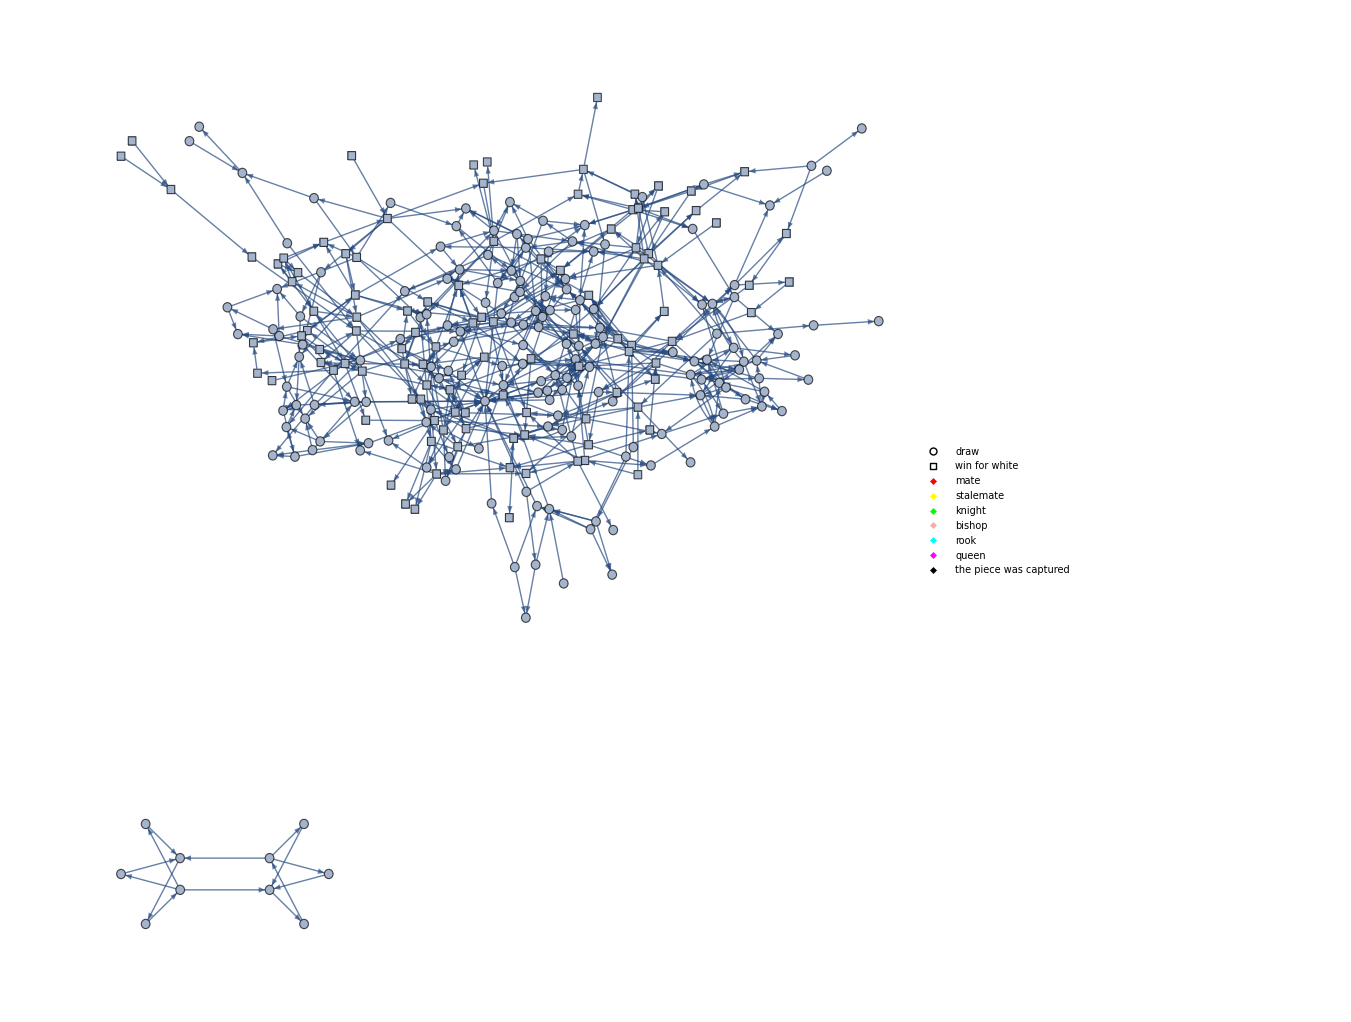

```mathematica
showWalk[graph,generateRandomWalk[3]]
```

```mathematica
generateResultsGraph[3]
```

-Graphics-

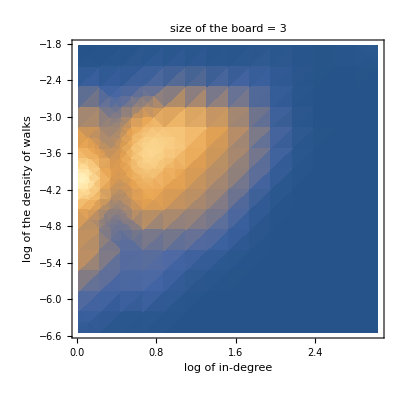

```mathematica
Module[{n=3},
g=generateGraph[n];
SmoothDensityHistogram[{Log@VertexInDegree[g],Log[VertexList[g]/.findExpectanciesPerNode[n]]}//Transpose,PlotLabel->"size of the board = "<>ToString[n],FrameLabel->{"log of in-degree", "log of the density of walks"}]
]
```

## Tree and multiway graph representations

```mathematica
generateTree[3,7]
```

-Graphics-

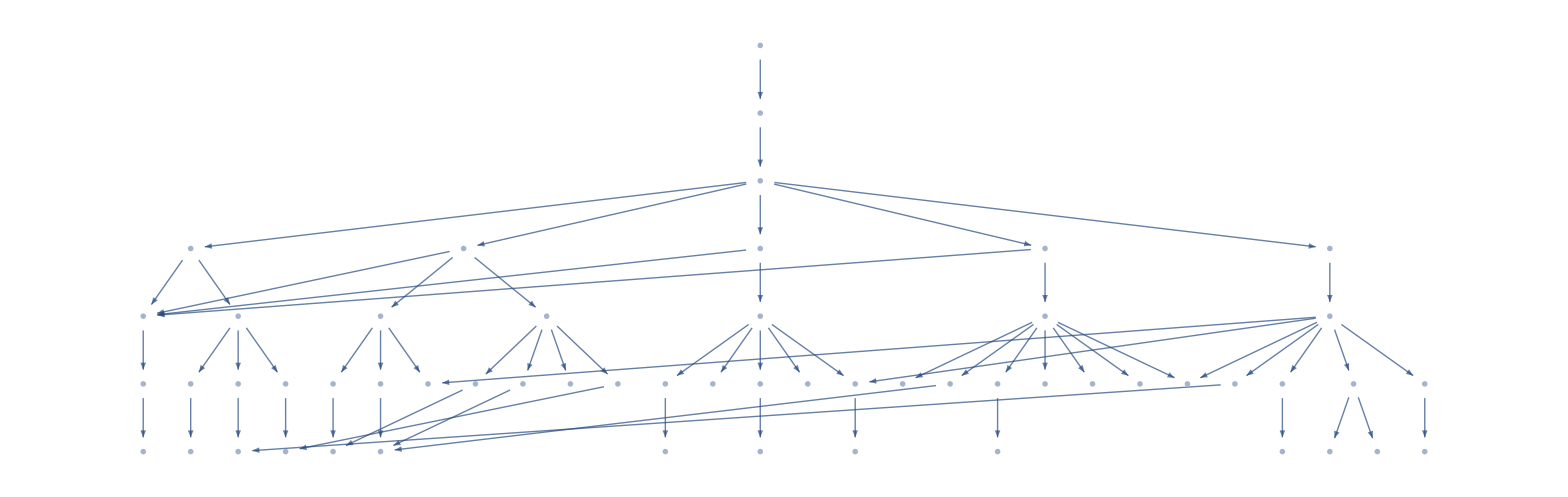

```mathematica
multiwayGraph[3,6]
```

## Asymptotics of the probability to win if moving randomly

```mathematica
(*winningProbability[3]*)
```

```mathematica
(*winningProbability[4]*)
```

```mathematica
(*winningProbability[5]*)
```

```mathematica
(*winningProbability[6]*)
```

FittedModel[1.29381-5.51513 x]

{1.29381-5.51513 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.29381 | 0.0912001 | 14.1864 | 0.0448011
x | -5.51513 | 0.056843 | -97.024 | 0.00656123}

1.29381-5.51513 Log[x]

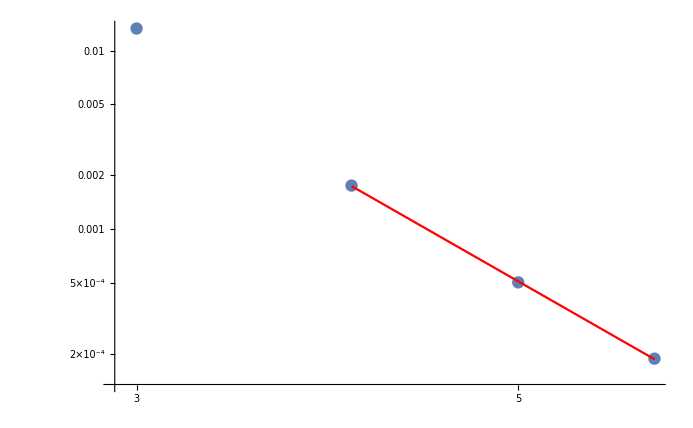

```mathematica
maxSize=6;
winningProbabilities={0.013327601428988655,0.0017540854000662885,0.0005025758583736119,0.00018770076682413694};
fit=LinearModelFit[{Log[Range[4,maxSize]],Log[Rest@winningProbabilities]}//Transpose,{1,x},x]
fit[{"BestFit","ParameterTable"}]
Normal[fit]/.x->Log[x]
Show[ListLogLogPlot[{Range[3,maxSize],winningProbabilities}//Transpose],LogLogPlot[Exp[Normal[fit]/.x->Log[t]],{t,4,maxSize},PlotStyle->Red]]
```

```mathematica
(*ResourceFunction["MultiwayDeletionsGraph"][generateGraph[3],{{{1,1},{3,2},{2,2},0,"pawn"}},10,VertexLabels->None]*)
```